```mathematica
(* --- TASK 1 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Xses = Range[0,120000,30000];
Yses = {9.81,9.7487,9.6879,9.6278,9.5682};
```

```mathematica
LagrangeFormula[nodes_,values_,x_]:=(
Basises = {};
CurrentI = 1;
Polinom = 0;
i=1;	
(*Calculate Basises*)
While[CurrentI ≠ Length[nodes] +1,
	CurrentBasis = 1;
	index =1;
	While[ index ≠Length[nodes] +1,
		If[CurrentI ≠ index,
			CurrentBasis = CurrentBasis * ((x -nodes[[index]])/(nodes[[CurrentI]] - nodes[[index]]));
		];
	
	index++
	];
AppendTo[Basises,CurrentBasis];
CurrentI ++;
];
(*Calculate Polinom*)
While[ i ≠ Length[values] +1,
	Polinom += values[[i]]*Basises[[i]];
i++;
];
Polinom
)
```

```mathematica
(* With only 2 nodes*)
```

```mathematica
P[x_] = LagrangeFormula[Xses[[2;;3]],Yses[[2;;3]],x] //Expand
```

9.8095-2.02667×10^-6 x

```mathematica
(* With All nodes *)
```

```mathematica
U[x_] = LagrangeFormula[Xses,Yses,x]//Expand
```

9.81-2.04611×10^-6 x-3.7037×10^-14 x^2+4.93827×10^-18 x^3-2.05761×10^-23 x^4

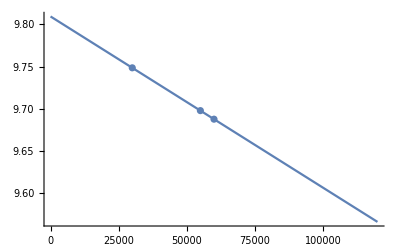

```mathematica
AppendTo[Yses,P[55000]];
AppendTo[Xses,55000];
Graphic = Plot[P[x],{x,0,120000}];
Dots =ListPlot[{{Xses[[2]],Yses[[2]]},{Xses[[3]],Yses[[3]]},{Xses[[6]],Yses[[6]]} }];
Show[Graphic,Dots]
```

```mathematica
(* --- TASK 2 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
H[x_]:=b0+b1*x+b2*x^2+b3*x^3+b4*x^4;
sol = NSolve[{H[0]== 1,H'[0]==0,H[1]==2,H'[1]==6,H[2]==21},{b0,b1,b2,b3,b4}]
H[x_]= H[x]/.sol[[1]]
```

{{b0→1.,b1→0.,b2→-3.,b3→4.,b4→0.}}

1.-3. x^2+4. x^3

```mathematica
(* --- TASK 3 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(* === POINT 1 ===================== *)
```

```mathematica
xS = Range[0,Pi/2,Pi/4];
yS = Table[Cos[x],{x,0,Pi/2,Pi/4}];
```

```mathematica
(* Lagrange Polynom - Иползвам функцията, която си направих по-горе за пресмятане на полиноми на Лагранж*)
```

```mathematica
CosPolinomLag[x_] = LagrangeFormula[xS,yS,x] //Expand //N
```

1.-0.109227 x-0.335749 x^2

```mathematica
(* === POINT 2 ===================== *)
```

```mathematica
(* ИМАМЕ възли 0 и π/2 и съответстващи им кратности 2 и 1. Тоест знаем че за възелът 0 трябва да имаме и първата производна в него. Така получаваме 3 условия. Също така знаем, че v0+v1-1= N, от където получаваме, че полиномът трябва да е от степен най-много 2. 

Имаме следните условия P(x)= cosx ; P(0)=1; P'(0)=0; P(π/2)=0;
 *)


(*разделени разлики*)
xSes = {0,0,π/2};
ySes = {1,0,0};
F[x_] = Cos[x];
```

```mathematica
Fx0 = ySes[[1]];
Fx1 = ySes[[1]];
Fx2 = ySes[[3]];
Fx0x1 = F'[xSes[[1]]];
Fx1x2 = (Fx2-Fx1)/(xSes[[3]]-xSes[[1]]);
Fx0x1x2 = (Fx1x2-Fx0x1)/(xSes[[3]]-xSes[[1]]);
```

```mathematica
(* Ermit Polynom *)
```

```mathematica
CosPolinomErmit[x_] = Fx0 + Fx0x1*(x-0) + Fx0x1x2(x-0)^2
```

1-(4 x^2)/π^2

```mathematica
(* === POINT 3 ===================== *)
```

```mathematica
(*Mistake by absolute value*)
```

```mathematica
MistakeWithLag[x_] =(F[x]-  CosPolinomLag[x])/F[x] //Abs;
MistakeWithErmit[x_] = (F[x]-CosPolinomErmit[x])/F[x] //Abs;
```

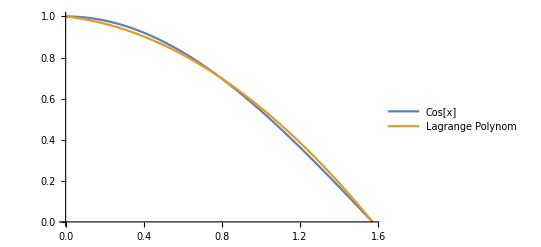

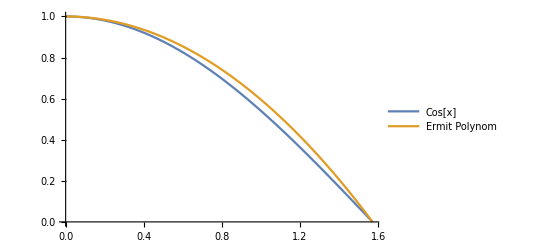

```mathematica
Plot[{F[x],CosPolinomLag[x]},{x,0,π/2},PlotLegends->{"Cos[x]","Lagrange Polynom"}]
Plot[{F[x],CosPolinomErmit[x]},{x,0,π/2},PlotLegends->{"Cos[x]","Ermit Polynom"}]
```

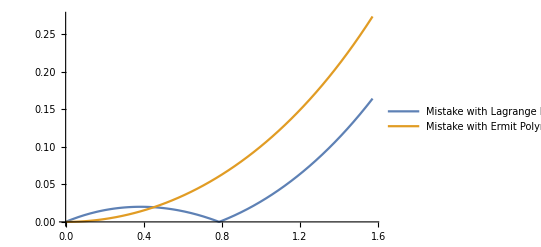

```mathematica
Plot[{MistakeWithLag[x],MistakeWithErmit[x]},{x,0,π/2},PlotLegends->{"Mistake with Lagrange Polynom", "Mistake with Ermit Polynom"}]
```

```mathematica
(* --- TASK 4 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(* === POINT 1 ===================== *)
```

```mathematica
G[x_]:=Sin[x] ;
Xs = {-1,-0.3,0.3,1};
```

```mathematica
R[x_,K_]=D[G[K],{K,4}]/(4!) (x-Xs[[1]])(x-Xs[[2]])(x-Xs[[3]])(x-Xs[[4]]) //Abs
```

1/24 Abs[(-1+x) (-0.3+x) (0.3+x) (1+x) Sin[K]]

```mathematica
(* За K ще изберем да е равно на 1 *)
```

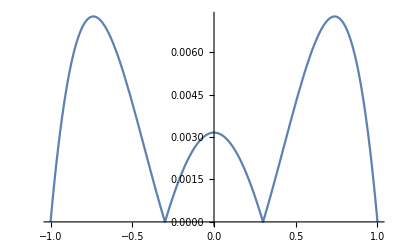

```mathematica
Plot[{R[x,Xs[[4]]]},{x,Xs[[1]],Xs[[4]]}]
```

```mathematica
(* === POINT 2 ===================== *)
chebishov = {};
n=3;
(*Чебишови възли*)
For[i=1, i<n+1, i++,
	AppendTo[chebishov, Cos[((2i-1)π)/(2*n)]]
]
chebishov;
Rch[x_,K_]=D[G[K],{K,n+1}]/((n+1)!) (x-chebishov[[1]])(x-chebishov[[2]])(x-chebishov[[3]]) //Abs
```

1/24 Abs[x (-(√3)/2+x) ((√3)/2+x) Sin[K]]

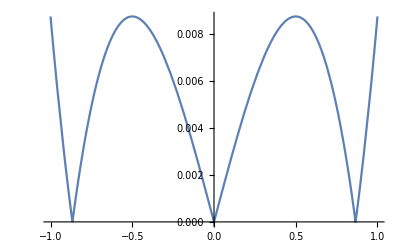

```mathematica
Plot[Rch[x,1],{x,-1,1}]
```

```mathematica
(* --- TASK 5 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
finalDiff[nodes_,values_]:=(
If[Length[nodes]==1,
values[[1]],
(finalDiff[nodes[[2;;Length[nodes]]],values[[2;;Length[nodes]]]]-finalDiff[nodes[[1;;Length[nodes]-1]],values[[1;;Length[nodes]-1]]])

]
)
newtonPolyForward[nodes_,values_,x_]:=(
poly=0;
product=1;
For[i=1,i≤Length[nodes],i++,
poly+=finalDiff[nodes[[1;;i]],values[[1;;i]]]*product;
product*=x-nodes[[i]]
];
poly//Expand
)
```

```mathematica
newtonPolyForward[{0,Pi/4,Pi/2},{0,Sin[Pi/4],Sin[Pi/2]},x]
```

x/(√2)-(π x)/4+(π x)/(2 √2)+x^2-√2 x^2

```mathematica
NewtonForward[n_,x0_,h_,f_]:=(

func=f;
F[x_] = func;

xs = Range[x0,x0+n*h,h];
ys = F[xs]//N;

newtonPolyForward[xs,ys,x]
)
```

```mathematica
NewtonForward[2,0,Pi/4,Sin[x]]
```

0.+1.16401 x-0.335749 x^2

```mathematica
(* --- TASK 6 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
dividedDiff[nodes_,values_]:=(
If[Length[nodes]==1,
values[[1]],
(dividedDiff[nodes[[2;;Length[nodes]]],values[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],values[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]])]
)
newtonPoly[nodes_,values_,x_]:=(
poly=0;
product=1;
For[i=1,i≤Length[nodes],i++,
poly+=dividedDiff[nodes[[1;;i]],values[[1;;i]]]*product;
product*=x-nodes[[i]]
];
poly//Expand
)
```

```mathematica
newtonPoly[{0,Pi/4,Pi/2},{0,Sin[Pi/4],Sin[Pi/2]},x]
```

-(2 x)/π+(4 √2 x)/π+(8 x^2)/π^2-(8 √2 x^2)/π^2

```mathematica
Newton[n_,x0_,h_,f_]:=(

func=f;
F[x_] = func;

xs = Range[x0,x0+n*h,h];
ys = F[xs]//N;

newtonPoly[xs,ys,x]
)

Newton[2,0,Pi/4,Sin[x]]
```

0.+1.16401 x-0.335749 x^2

```mathematica
(* --- TASK 7 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Lagrange[n_,x0_,h_,f_]:=(

func=f;
F[x_] = func;

xs = Range[x0,x0+n*h,h];
ys = F[xs]//N;

Basises = {};
CurrentI = 1;
Polinom =0;
i=1;	
(*Calculate Basises*)
While[CurrentI ≠ Length[xs] +1,
	CurrentBasis = 1;
	index =1;
	While[ index ≠Length[xs] +1,
		If[CurrentI ≠ index,
			CurrentBasis = CurrentBasis * ((x -xs[[index]])/(xs[[CurrentI]] - xs[[index]]));
		];
	
	index++
	];
AppendTo[Basises,CurrentBasis];
CurrentI ++;
];
(*Calculate Polinom*)
While[ i ≠ Length[ys] +1,
	Polinom += ys[[i]]*Basises[[i]];
i++;
];
Polinom
)
```

```mathematica
Lagrange[2,0,Pi/4,Sin[x]]//Expand
```

0.+1.16401 x-0.335749 x^2

```mathematica
(* --- TASK 8 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
T[x_] := a0 + a1*Cos[x] + a2*Sin[x] +a3*Cos[2x] + a4*Sin[2x];
t= Range[0,2.5,0.5];
t = Delete[t,2];
ms = {0,1,1.5,4,2};
```

```mathematica
periodT =3;
periodSin = 2π;
```

```mathematica
t1 = periodSin/periodT t ;
```

```mathematica
sol = NSolve[{T[t1[[1]]] ==  ms[[1]],T[t1[[2]]] ==  ms[[2]],T[t1[[3]]] ==  ms[[3]],T[t1[[4]]] ==  ms[[4]],T[t1[[5]]] ==  ms[[5]] },{a0,a1,a2,a3,a4}   ]
```

{{a0→1.66667,a1→-0.75,a2→-1.01036,a3→-0.916667,a4→0.721688}}

```mathematica
T[x_] = T[x] /.sol[[1]]
```

1.66667-0.75 Cos[x]-0.916667 Cos[2 x]-1.01036 Sin[x]+0.721688 Sin[2 x]

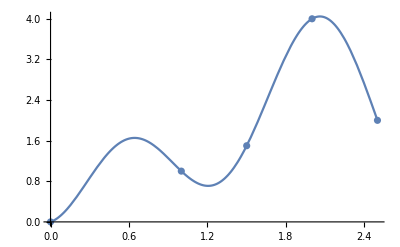

```mathematica
plot = Plot[T[(2π)/3 x],{x,t[[1]],t[[5]]}];
dots = ListPlot[{{t[[1]],ms[[1]]},{t[[2]],ms[[2]]},{t[[3]],ms[[3]]},{t[[4]],ms[[4]]},{t[[5]],ms[[5]]}}];
Show[plot,dots]
```

```mathematica
(* --- TASK 9 ------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(* базисите 1,2,3 не са възмжни за тези данни, тъй като нашата функция очевидно ще намалява. 6 също не е възможно, защото в знаменател имаме n-x като n e [1,4]. В такъв случай при съставяне на системата ще се получи знаменател = 0, по-точно в точките x=2 и x=4, което не е възможно. За това ни остават възможности 4 и 5. Ще представим и двете.  *)
```

```mathematica
(* За базис {1, E^(=x),E^(=2x),E^(=3x),E^(=4x)} *)
```

```mathematica
M[x_] := a0 + a1*E^-x + a2*E^(-2x) +a3*E^(-3x) + a4*E^(-4x);
th = Range[0,8,2];
c = {0.1,0.009,0.0011,0.00003, 0.0000012};
```

```mathematica
solve = NSolve[{M[th[[1]]] ==  c[[1]],M[th[[2]]] ==  c[[2]],M[th[[3]]] == c[[3]],M[th[[4]]] ==  c[[4]],M[th[[5]]] ==  c[[5]]},{a0,a1,a2,a3,a4}];
M[x_] = M[x]/.solve[[1]]
```

-4.18801×10^-7+22.3483 ⅇ^(-4 x)-25.7986 ⅇ^(-3 x)+3.54666 ⅇ^(-2 x)+0.00363871 ⅇ^-x

```mathematica
(* За базис {1,1/(1-x),1/(2-x),1/(3-x),1/(4-x)}*)
```

```mathematica
B[x_] := a0 + a1/(1+x) + a2/(2+x) +a3/(3+x) + a4/(4+x)
```

```mathematica
solve1 = NSolve[{B[th[[1]]] ==  c[[1]],B[th[[2]]] ==  c[[2]],B[th[[3]]] == c[[3]],B[th[[4]]] ==  c[[4]],B[th[[5]]] ==  c[[5]]},{a0,a1,a2,a3,a4}];
B[x_]= B[x]/.solve1[[1]]
```

-0.000162875+0.0872747/(1+x)+1.33087/(2+x)-3.70733/(3+x)+2.33292/(4+x)

```mathematica
(*Графики на 2-та получени полинома*)
```

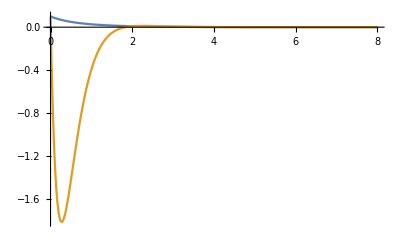

```mathematica
Plot[{B[x],M[x]},{x,0,8}, PlotRange->Full]
```

```mathematica
(* Оказва се, че при първият вариант (5), в точките от 0 до 2 се получават отрицателни стойности, което според зададените данни не е възможно. За това верният отговор е (4) *)
```

```mathematica
B[x]
```

-0.000162875+0.0872747/(1+x)+1.33087/(2+x)-3.70733/(3+x)+2.33292/(4+x)